# ExactCover`

### Author

Jan G. Korvink © 2013, ..., 2021

This package solves the exact cover problem of computer science using Donald Knuth's dancing links search algorithm. Given a sparsely occupied integer boolean matrix (entries are either ones or naughts), we look for subsets of matrix rows that cover all the columns, i.e., each column has only one nonzero entry.

ExactCover[ matrix ] | finds all subsets of rows of the rectangular matrix which have exactly one nonzero element in each column.

Exact cover function.

First we import the package:

```mathematica
<<(NotebookDirectory[]<>"ExactCover.m")
```

Now we define a simple matrix:

```mathematica
mat=({{0, 0, 1, 0, 1, 1, 0}, {1, 0, 0, 1, 0, 0, 1}, {0, 1, 1, 0, 0, 1, 0}, {1, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 1, 0, 1}});
```

Here we compute its exact cover:

```mathematica
sol=ExactCover[mat]
```

{{{1,4},{3,5,6},{2,7}}}

The algorithm has returned a single solution of three matrix rows. We see that the matrix lines are given in a sparse format by only listing the column numbers in each line. We can directly use the data to check the correctness of the algorithm. First we flatten and sort the solution, and check it with a complete range of numbers equal to the number of columns in the original matrix:

```mathematica
Map[(Sort[Flatten[#]]==Range[7])&,sol]
```

{True}

If we want, we can use one of the solutions and construct its associated exact cover matrix:

```mathematica
Map[Normal[SparseArray[#,{7}]]&,Map[(#->1)&,sol,{3}],{2}]
```

{{{1,0,0,1,0,0,0},{0,0,1,0,1,1,0},{0,1,0,0,0,0,1}}}

Here we see that it is indeed an exact cover subset, since each column only has one nonzero element:

```mathematica
Map[MatrixForm,%]
```

{(1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1)}

The solution to a number of games can be computed using the exact cover algorithm. For example, pentomino and other tilings, the eight queens problem (see below), as well as the sudoku game fit into this category. Applications usually require a preprocessing step that create an appropriate matrix, as well as a postprocessing step to extract the relevant data/meaning from the solution.

Option | default | Description
PlotAlgorithm | False | Plot the progress of the dancing links algorithm using a graphic.

We can follow the progress of the algorithm by switching on a plotting function of the linked data structure. Here we do it for a small problem so as to avoid generating too much graphical output:

```mathematica
ExactCover[({{0, 0, 1}, {0, 1, 1}, {1, 0, 0}, {0, 1, 0}}),PlotAlgorithm->True]
```

{{{1},{2,3}},{{1},{2},{3}}}

In the plots above, the yellow dots are data nodes, the green dots column header nodes, and the blue dot the root pointer.

Application of Exact Cover to Solving the Latin Square Puzzle

The latin square of size n is an n×n square, each row and column containing the numbers 1 to n once only. We can solve this puzzle as an exact cover problem as follows. We construct a matrix that has a coumn for each digit from 1 to n, coupled with each line and column position, and a column for each cell in the puzzle. Thus we have 3 n^2 columns. For a possible digit d in the position {r,c} of the puzzle, we hence construct a matrix line with three nonzero entries, for the row in position (d-1)n+r, for the column in position (d-1)n+c+n^2, and for the cell entry in position (r-1)n+c+2 n^2. From the row and column positions we can easily generate a consecutive cell number:

```mathematica
rcToEntry[r_,c_,n_]:=(Quotient[r-1,1]n)+(Quotient[c-1,1]+1);
```

Let us test this code by applying it to a table of indices:

```mathematica
Table[rcToEntry[i,j,3],{i,1,3},{j,1,3}]
```

{{1,2,3},{4,5,6},{7,8,9}}

A constraint line is best built up from three parts each of length n^2. Here my simple code for these pieces based on sparse matrix representations (r, c, d stand for row, column and digit of the original puzzle):

```mathematica
generalConstraint[p_,n_]:=Normal[SparseArray[{p->1},n^2]];
rowConstraint[r_,d_,n_]:=generalConstraint[((d-1)n+r),n];
columnConstraint[c_,d_,n_]:=generalConstraint[((d-1)n+c),n];
cellConstraint[{r_,c_},n_]:=generalConstraint[rcToEntry[r,c,n],n];
```

The following code will now generate the complete matrix:

```mathematica
makeLatinSquareMatrix[n_]:=Flatten[Table[Join[rowConstraint[r,d,n],columnConstraint[c,d,n],cellConstraint[{r,c},n]],{d,1,n},{r,1,n},{c,1,n}],2];
```

Let us try  the code for a small yet trivial problem:

```mathematica
makeLatinSquareMatrix[2]//MatrixForm
```

(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1)

The exact cover solver finds the lines corresponding to a solution:

```mathematica
ExactCover[makeLatinSquareMatrix[2]]
```

{{{1,5,9},{2,6,12},{3,8,10},{4,7,11}},{{1,6,10},{2,5,11},{3,7,9},{4,8,12}}}

Since the solution will be in sparse format, we need a function to reconstruct the latin square:

```mathematica
extractLatinSquare[sol:{{(_Integer)..}..}]:=Module[{n},
n=Sqrt[Length[sol]];
Normal[
SparseArray[
Map[
With[{r=Mod[#[[1]]-1,n]+1,
c=Mod[#[[2]]+1,n]+1,
d=Quotient[#[[1]]-1,n]+1},
{r,c}->d
]&,
sol],
{n,n}]
]
];
```

Applying this function to the solution gives a list of matrices:

```mathematica
Map[extractLatinSquare[#]&,ExactCover[makeLatinSquareMatrix[2]]]
```

{{{1,2},{2,1}},{{2,1},{1,2}}}

It is more convienient to have a plotting program for solutions:

```mathematica
plotSolution[sol:{{(_Integer)..}..}]:=Module[{n},
n=Sqrt[Length[sol]];
Graphics[
MapIndexed[With[{r=#2[[1]],c=#2[[2]],d=#1},
{Line[{{r-.5,c-.5},{r-.5,c+.5},{r+.5,c+.5},{r+.5,c-.5},{r-.5,c-.5}}],Text[d,{r,c}]}
]&,sol,{2}],
AspectRatio->Automatic,PlotRange->All]
];
```

It is now a simple matter to solve for the twelve solutions of the 3×3 magic squares problem and to plot them:

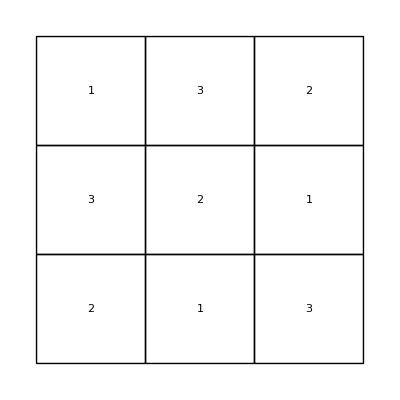
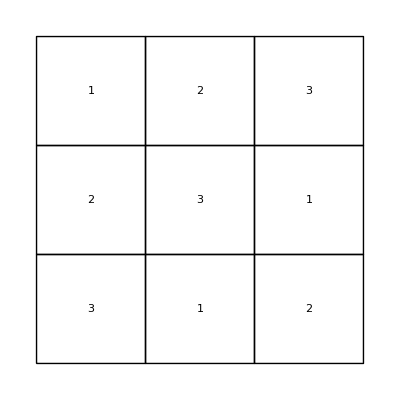
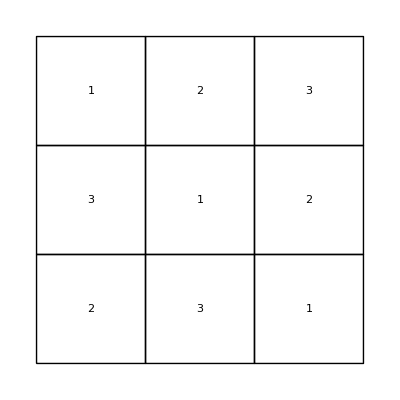
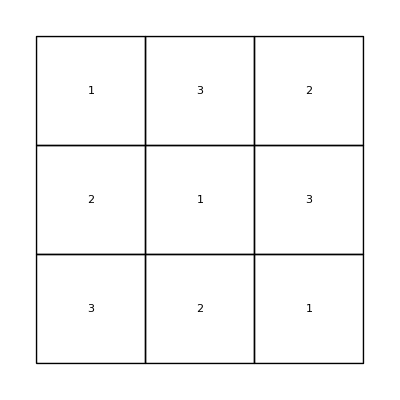
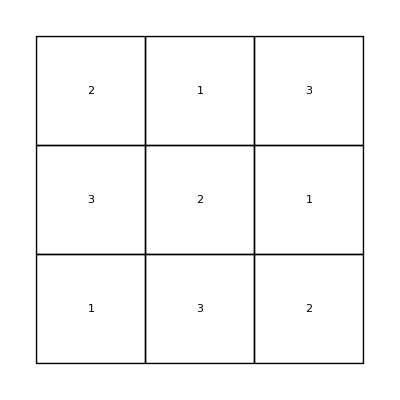
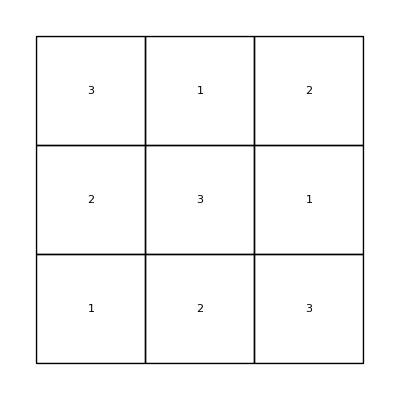
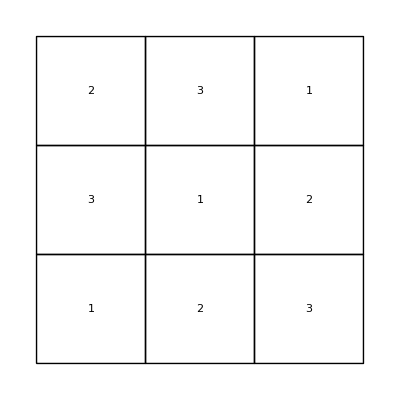
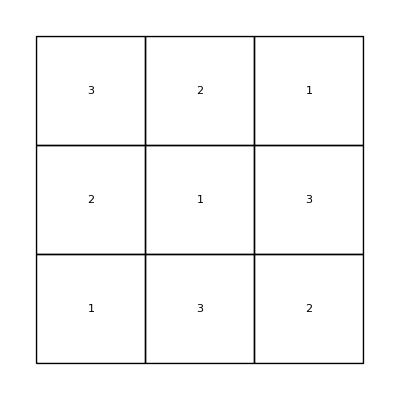

```mathematica
Map[Show[plotSolution[extractLatinSquare[#]]]&,ExactCover[makeLatinSquareMatrix[3]]]
```

Watch out, though, when trying to automatically plot all solutions, as the number of these grow real fast for latin squares of sizes 4 and above:

```mathematica
Table[Length[ExactCover[makeLatinSquareMatrix[i]]],{i,1,4}]
```

{1,2,12,576}

It is safer to first compute the matrix of solutions and then only to plot a few of them:

{0.780396,Null}

{576,4,4}

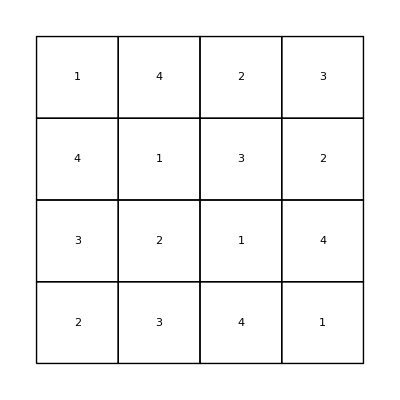

```mathematica
Timing[s=extractLatinSquare[#1]&/@
             ExactCover[makeLatinSquareMatrix[4]];]
Dimensions[s]
Show[plotSolution[s⟦RandomInteger[{1, 576}]⟧]]
```

Application of Exact Cover to Solving the 8 Queens Puzzle

[Begin Wikipedia quote] Consider a matrix with one column for each of the n ranks of the board, one column for each of the n files, and one column for each of the 4n-6 nontrivial diagonals of the board. The matrix has n^2 rows: one for each possible queen placement, and each row has a 1 in the columns corresponding to that square's rank, file, and diagonals and a 0 in all the other columns. Then the n queens problem is equivalent to choosing a subset of the rows of this matrix such that every column has a 1 in precisely one of the chosen rows; this is an exact cover problem. [end Wikipedia quote]

Actually, the Wikipedia entry contains an error in the argumentation. On an n by n board, we will place at most n queens. They will avoid each other by being in separate rows and columns. But we have a total of 2n-3 parallel diagonals which have to be guarded by the n queens. Which means that all diagonals will not be occupied. The exact cover procedure will not find any solutions. So, in order to turn the problem into a correct exact cover problem, we will add 4n-6 lines with a 1 only in each of the columns corresponding to the diagonals. This will allow the algorithm to complete its search for a complete cover by adding these rows, which we can then delete afterwards (these will be the only rows with only a single column entry).

In order to set up the problem, we need to associate each {r,c} position on the board not only with its row and column, but also with its uniquely numbered nontrivial diagonal, and with its unique cell number. The latter is easy:

```mathematica
fromRC[r_,c_,n_]:=(r-1)n+c;
```

As for numbering the diagonals, first we start with the ones running Northwest to Southeast. There are 2n-3 of these. An appropriate sum of the row and column indices does the trick as these simple lines of code show:

```mathematica
n=4;Table[i-j+n-1,{i,1,n},{j,1,n}]//MatrixForm
Table[i +j+(2n-5),{i,1,n},{j,1,n}]//MatrixForm
```

(3 | 2 | 1 | 0
4 | 3 | 2 | 1
5 | 4 | 3 | 2
6 | 5 | 4 | 3)

(5 | 6 | 7 | 8
6 | 7 | 8 | 9
7 | 8 | 9 | 10
8 | 9 | 10 | 11)

It is of course best to turn the above into a procedure that generates the line entry for a given board square:

```mathematica
matrixLine[r_,c_,n_]:=Module[{d1,d2},
(* Which diagonal 2 *)
If[{r,c}=={1,1}||{r,c}=={n,n},d2={},
d2={r +c+(2n-5)}];
(* Which diagonal 1 *)
If[{r,c}=={1,n}||{r,c}=={n,1},d1={},
d1={r-c+n-1}];
(* Put them together *)
Normal[SparseArray[Map[(#->1)&,Join[d1,d2,(4n-6)+{r,n+c}]],(6n-6)]]
];
```

Now it is a straightforward matter to build the whole matrix (note that we add 4n-6 diagonal lines at the end):

```mathematica
queensProblemMatrix[n_]:=Join[Flatten[Table[matrixLine[i,j,n],{i,1,n},{j,1,n}],1],
Table[Normal[SparseArray[i->1,(6n-6)]],{i,1,(4n-6)}]
];
```

This is what the matrix looks like. It has 6n-6 columns and n^2+4n-6 rows:

```mathematica
queensProblemMatrix[4]
```

{{0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1},{0,0,0,1,0,1,0,0,0,0,0,1,0,0,1,0,0,0},{0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0},{0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0},{0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}}

This matrix can now be solved as an exact cover problem. Note the appearance of the single diagonal lines as lists with a singly entry, in this case, two occurrences for each solution:

```mathematica
ExactCover[queensProblemMatrix[4]]
```

{{{1,7,11,17},{4,6,12,15},{8},{2,10,13,18},{3},{5,9,14,16}},{{1,9,12,18},{4,10,14,17},{8},{5,7,13,15},{3},{2,6,11,16}}}

From the literature, we know that the 8 queens problem has 92 unique solutions. Our algorithm seems to find them all, so we feel that we are on the right road:

```mathematica
Table[{i,Length[ExactCover[queensProblemMatrix[i]]]},{i,4,8}]
```

{{4,2},{5,10},{6,4},{7,40},{8,92}}

Let us now construct a procedure for extracting the solutions. First we drop line entries with only one column. Of the remaining matrix row entries, the last two pick out the approapriate row and column, from which we simply have to subtract the table offset. Our choice is to make such an entry into a sparse entry specification:

```mathematica
convertLine[l_List,n_Integer]:={(#[[-2]]-(4n-6)),(#[[-1]]-(4n-6)-n)}->1&/@(Select[l,(Length[#1]>1)&]);
```

Now we pack all of this into a function and add the conversion from sparse to normal format:

```mathematica
solveQueensProblem[n_]:=Map[Normal[SparseArray[convertLine[#,n],{n,n}]]&,ExactCover[queensProblemMatrix[n]]];
```

Let us try this for a 4 by 4 chessboard:

```mathematica
solveQueensProblem[4]
```

{{{0,0,1,0},{1,0,0,0},{0,0,0,1},{0,1,0,0}},{{0,1,0,0},{0,0,0,1},{1,0,0,0},{0,0,1,0}}}

What remains is to make the solution nice and graphic. Here a procedure to plot the board. The term OddQ[i+ j] generates the chessboard pattern as a True/False array:

```mathematica
drawBoard[b:{{(_Integer)..}..}]:=Module[{n},
n=Length[b];
Graphics[{
Table[If[OddQ[i+ j],{RGBColor[0,1,0],Rectangle[{i-.5,j-.5},{i+.5,j+.5}]},{}],{i,1,n},{j,1,n}],
Table[If[b[[i,j]]==1,{GrayLevel[.9],Disk[{i,j},.25],RGBColor[1,0,0],Circle[{i,j},.25],Text["Q",{i,j}]},{}],{i,1,n},{j,1,n}],{GrayLevel[0],Line[{{0.5,0.5},{n+0.5,0.5},{n+0.5,n+0.5},{0.5,n+0.5},{0.5,0.5}}]}},AspectRatio->Automatic,PlotRange->All]
];
```

Applying the plotting procedure to the solutions list gives us a nice intuitive picture from which to verify the correctness of each solution:

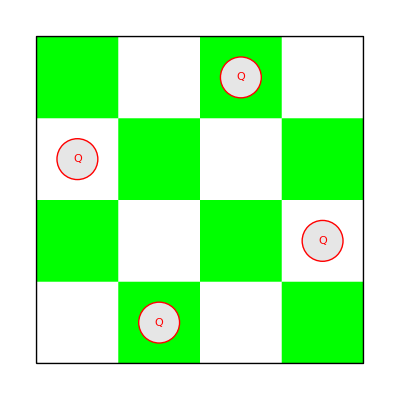
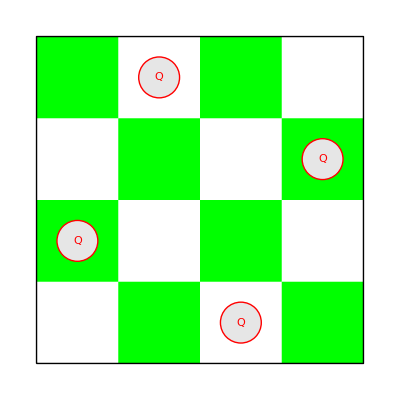

```mathematica
Show[drawBoard[#]]&/@solveQueensProblem[4]
```

The famous 8-queens problem is now easily solved. The pictures of the 92 solutions consume quite a bit of memory:

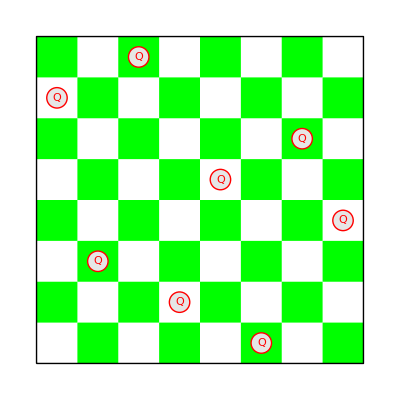
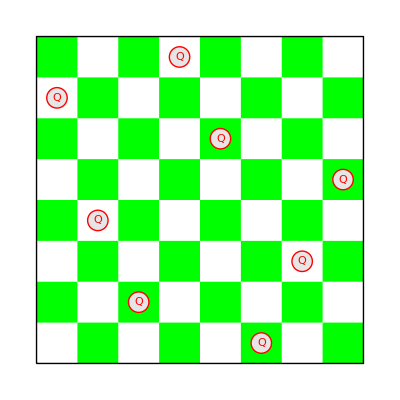
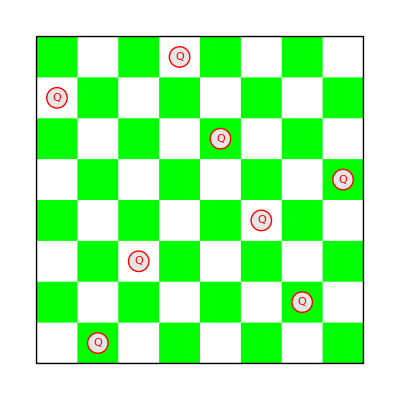
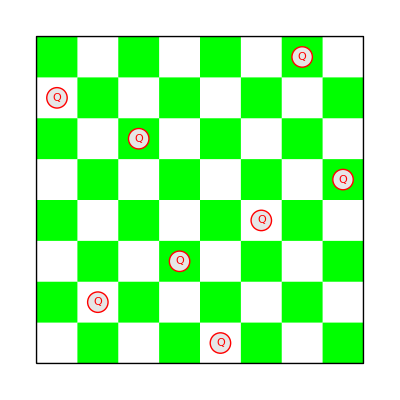
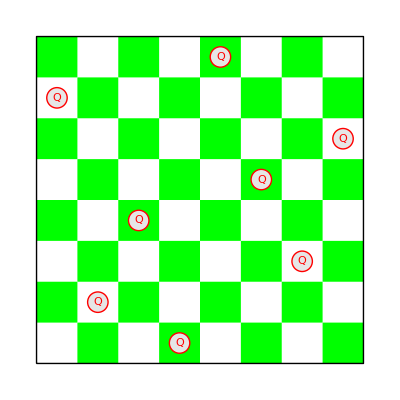
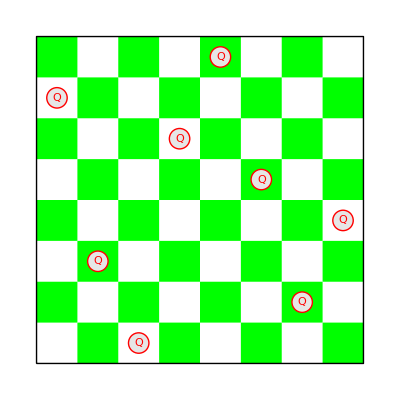
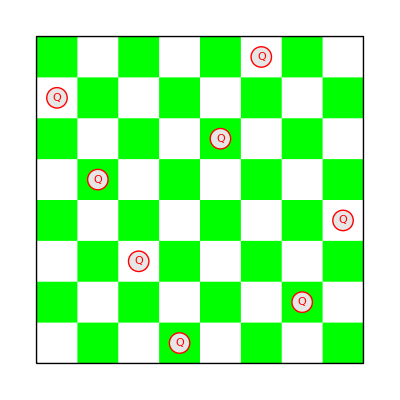
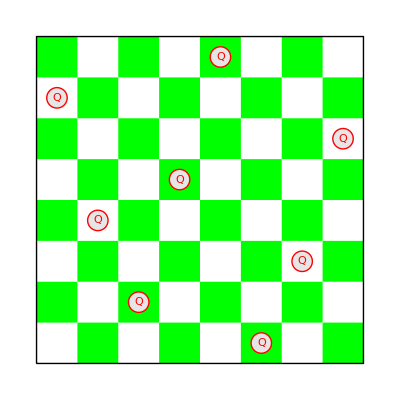

```mathematica
Show[drawBoard[#]]&/@solveQueensProblem[8]
```